```mathematica
NS["maxent_pop_or_sample_v2a.nb"]
```

```mathematica
(* assumptions *)
assu=(Element[nn||rr||n||r||m,Integers]&&nn≥n≥1&&0≤rr≤nn&&0≤r≤n&&0≤m≤n&&0<k<1&&0<a<1&&0<aa<1&&nn*aa≥n*a&&aa≥k*a);
```

```mathematica
(* hypergeometric distribution for sample given population, eqn (8) *)

Clear[condp2];condp2[n_,a_,nn_,aa_]:=(N@Binomial[n,a]*N@Binomial[nn-n,aa-a]/N@Binomial[nn,aa])
```

```mathematica
Clear[condp];condp[n_,a_,nn_,aa_]:=(Binomial[n,a]*Binomial[nn-n,aa-a]/Binomial[nn,aa]//N)
```

```mathematica
(* load values already calculated of the hypergeometric distribution *)
Import[$HomeDirectory<>"\\work\\largefiles\\condp.zip","*"];
```

```mathematica
(* save values already calculated of the hypergeometric distribution *)Save["condp.m",condp]
```

```mathematica
ClearAll[nn,j1,j2,rann];nn=5000;j2=5.696/nn;j1=-nn*j2*28/100-Log[nn*j2]*72/100;(*j1=-2550/nn;*)rann=(Range[0,nn]/nn);{j1,j2,l1=j1*nn,l2=j2*nn*(nn-1)/2}//N
```

{-2.84751,0.0011392,-14237.6,14237.2}

```mathematica
Clear[qq];qq=Block[{list=Table[mep[rr,nn,l1,l2],{rr,0,nn}]//N},list/Total[list]];
```

```mathematica
{a1=Table[rr/nn,{rr,0,nn}].qq//N,a2=Table[rr*(rr-1)/(nn*(nn-1)),{rr,0,nn}].qq//N}
```

$Aborted[]

```mathematica
ListPlot[T@{rann,qq*nn}, Joined->True,PlotRange->All]
```

```mathematica
ListLogPlot[T@{rann,qq*nn}, Joined->True]
```

```mathematica
ni=200;qqmar=Block[{list=Table[condp[ni,r,nn,rr],{r,0,ni},{rr,0,nn}].(qq//N)},list/Total[list]];
```

```mathematica
ni=200;ran=(Range[0,ni]/ni);ListLogPlot[{T@{ran,qqmar*ni},T@{rann,qq*nn}}, Joined->True]
```

```mathematica
ListPlot[{T@{ran,qqmar*ni},T@{rann,qq*nn}}, Joined->True,PlotRange->All]
```

```mathematica
<<"scripts/ME_homsolution.m"
```

```mathematica
a1=Table[rr/nn,{rr,0,nn}].qq//N
```

0.432501

```mathematica
a2=Table[rr*(rr-1)/(nn*(nn-1)),{rr,0,nn}].qq//N
```

0.353175

```mathematica
{zj1,zj2,qqx}=MEhomsolution[a1,a2,ni,30][[1;;3]];
```

```mathematica
ListLogPlot[{T@{ran,qqx*ni},T@{ran,qqmar*ni}}, Joined->True,PlotStyle->{{blue,Dashed,Thick},red}]
```

```mathematica
ListPlot[{T@{ran,qqx*ni},T@{ran,qqmar*ni}}, Joined->True,PlotStyle->{{blue,Dashed,Thick},red},PlotRange->All]
```

```mathematica
(* Define various symbols to be used in plots *)
```

```mathematica
sidesquare=2*Sqrt[3]*3/8
```

(3 √3)/4

```mathematica
radiuscircle=Sqrt[(2*Sqrt[3]*3/2)/Pi];
```

```mathematica
radiuscircle=2*Sqrt[3]*3/(2*Pi);
```

```mathematica
size=2;absoluteThickness=1;
emptySquare=Graphics[{AbsoluteThickness[absoluteThickness],JoinedCurve[Line[{Offset[size {sidesquare,sidesquare}],Offset[size {-sidesquare,sidesquare}],Offset[size {-sidesquare,-sidesquare}],Offset[size {sidesquare,-sidesquare}]}],CurveClosed->True]},AlignmentPoint->{0,0}];
emptyUpTriangle=Graphics[{AbsoluteThickness[absoluteThickness],JoinedCurve[Line[{Offset[size {0,2}],Offset[size {Sqrt[3],-1}],Offset[size {-Sqrt[3],-1}]}],CurveClosed->True]},AlignmentPoint->{0,0}];
filledUpTriangle=Graphics[{Triangle[{Offset[size {0,2}+absoluteThickness {0,1}],Offset[size {Sqrt[3],-1}+absoluteThickness {Sqrt[3/4],-1/2}],Offset[size {-Sqrt[3],-1}+absoluteThickness {-Sqrt[3/4],-1/2}]}]},AlignmentPoint->{0,0}];
{emptyLeftTriangle,filledLeftTriangle,emptyDownTriangle,filledDownTriangle,emptyRightTriangle,filledRightTriangle}=Flatten[{emptyUpTriangle,filledUpTriangle}/.{x_?NumericQ,y_?NumericQ}:>RotationTransform[#][{x,y}]&/@{Pi/2,Pi/3,-Pi/2}];
emptyCircle=Graphics[{AbsoluteThickness[absoluteThickness],Circle[{0,0},Offset[size*radiuscircle+absoluteThickness]]},AlignmentPoint->{0,0}];
```

```mathematica
(* **** USED IN PAPER **** *)




(* First example: network of 5000 units, subnetwork of 200 *)
```

```mathematica
(* load scripts to calculate homogeneous maximum-entropy Lagrange multipliers *)
```

```mathematica
<<($HomeDirectory<>"/work/scripts/ME_homsolution2.m")
```

```mathematica
<<($HomeDirectory<>"/work/scripts/ME_homsolution.m")
```

```mathematica
(* choose constraints *)
N[{aa1,aa2,aa3,aa4}={478/10000,257/100000,148/1000000,881/100000000},3]
```

{0.0478,0.00257,0.000148,8.81×10^-6}

```mathematica
nn=5000;rann=Range[0,nn];
```

```mathematica
(* find Lagr multipliers, 2 constraints *)
{zj1,zj2,qq2ex,norm2}=MEhomsolution[aa1,aa2,nn,60];
```

```mathematica
Total[(qq2ex-pdf[5000])^2]
```

0.

```mathematica
(* compare higher moments *)
{{aa1,aa2,aa3,aa4},Table[(Binomial[rann,i].qq2)/Binomial[nn,i],{i,4}]}//T//MF//N
```

(0.0478 | 0.0478
0.00257 | 0.00257
0.000148 | 0.000406222
8.81×10^-6 | 0.000289783)

```mathematica
(* marginalize to subnetwork of 200 units*)
ni=200;ran=Range[0,ni];qqmarex=Block[{list=ParallelTable[Table[condp[ni,r,nn,rr],{rr,0,nn}].qq2ex,{r,0,ni},Method->"CoarsestGrained"]},list/Total[list]];
```

```mathematica
Total[(qqmarex-qqmarg[5000])^2]
```

3.40602×10^-33

```mathematica
(* compare higher moments *)
{{aa1,aa2,aa3,aa4},Table[(Binomial[ran,i].qqmar)/Binomial[ni,i],{i,4}]}//T//MF//N
```

(0.0478 | 0.0478
0.00257 | 0.00257
0.000148 | 0.000404437
8.81×10^-6 | 0.0002878)

```mathematica
(* maxent directly at subpopulation level *)

ni=200;ran=Range[0,ni];{zj1x,zj2x,qqx,norm2x}=MEhomsolution[aa1,aa2,ni,60];
```

```mathematica
(* compare higher moments *)
{{aa1,aa2,aa3,aa4},Table[(Binomial[ran,i].qqx)/Binomial[ni,i],{i,4}]}//T//MF//N
```

(0.0478 | 0.0478
0.00257 | 0.00257
0.000148 | 0.000317526
8.81×10^-6 | 0.000191017)

```mathematica
listpops1={5000,6000,7000,8000,9000,10000};Do[Print[nnn];
{zj1d,zj2d,qqq}=MEhomsolution[aa1,aa2,nnn,60][[1;;3]];
pdf[nnn]=qqq;
themarginal=
Block[{list=ParallelTable[Table[condp2[ni,r,nnn,rr],{rr,0,nnn}].qqq,{r,0,ni},Method->"CoarsestGrained"]},list/Total[list]];
qqmarg[nnn]=themarginal;
Save["margsaved_"<>ToString[nnn]<>".m",{qqq,themarginal}];
,{nnn,listpops1}]
```

$Aborted

```mathematica
listpops1={5000,6000,7000,8000,9000,10000};Do[Print[nnn];
{zj1d,zj2d,qqq}=MEhomsolution[aa1,aa2,nnn,60][[1;;3]];
pdf[nnn]=qqq;
themarginal=
Block[{list=ParallelTable[Table[condp2[ni,r,nnn,rr],{rr,0,nnn}].qqq,{r,0,ni},Method->"CoarsestGrained"]},list/Total[list]];
qqmarg[nnn]=themarginal;
Save["margsaved_"<>ToString[nnn]<>".m",{qqq,themarginal}];
,{nnn,listpops1}]
```

```mathematica
listpops2={1000,2000,3000,4000};
Do[Print[nnn];
{zj1d,zj2d,qqq}=MEhomsolution[aa1,aa2,nnn,60][[1;;3]];
pdf[nnn]=qqq;
themarginal=
Block[{list=ParallelTable[Table[condp2[ni,r,nnn,rr],{rr,0,nnn}].qqq,{r,0,ni},Method->"CoarsestGrained"]},list/Total[list]];
qqmarg[nnn]=themarginal;
Save["margsaved_"<>ToString[nnn]<>".m",{qqq,themarginal}];
,{nnn,listpops2}]
```

```mathematica
(* Read marginal distributions from different superpop sizes from file *)listpops={1000,2000,3000,4000,5000,6000,7000,8000,9000,10000};
Do[Print[nnn];
<<($HomeDirectory<>"/work/"<>"margsaved_"<>ToString[nnn]<>".m");
pdf[nnn]=qqq;
qqmarg[nnn]=themarginal;
,{nnn,listpops}]
```

```mathematica
qqmar=qqmarg[10000];
```

```mathematica
fweights[a_]:=1/a;weights[nnn_]=fweights[nnn]/Sum[fweights[nnnn],{nnnn,listpops}];
```

```mathematica
qqmix=Sum[qqmarg[nnn]*weights[nnn],{nnn,listpops}];
```

```mathematica
ClearAll[fweights2];fweights2[a_]:=1;weights2[nnn_]=fweights2[nnn]/Sum[fweights2[nnnn],{nnnn,listpops}];
```

```mathematica
qqmix2=Sum[qqmarg[nnn]*weights2[nnn],{nnn,listpops}];
```

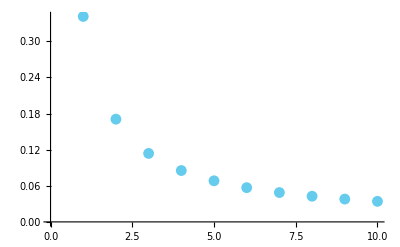

```mathematica
ListPlot[Table[weights[a],{a,listpops}]]
```

```mathematica
(* ENTROPIES *)
{-qqx.Log[qqx],-qqmar.Log[qqmar],-qqmix.Log[qqmix]}//N
```

{2.68159,2.51922,2.53617}

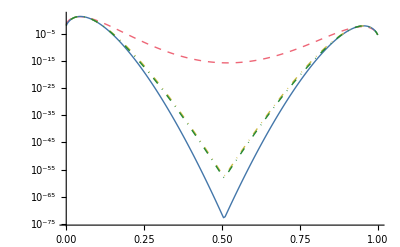

```mathematica
ListLogPlot[{T@{ran/ni,qqx*ni},T@{ran/ni,qqmar*ni},T@{ran/ni,qqmix*ni},T@{ran/ni,qqmix2*ni}}, Joined->True,PlotStyle->{{red,Dashed,Thick},purpleblue,{yellow,DotDashed,Thick},{green,DotDashed,Thick}},PlotRange->All]
```

```mathematica
sidesquare=2*Sqrt[3]*3/8;radiuscircle=Sqrt[(2*Sqrt[3]*3/2)/Pi];
(*radiuscircle=2*Sqrt[3]*3/(2*Pi);*)

size=1.5;absoluteThickness=1;
emptySquare=Graphics[{AbsoluteThickness[absoluteThickness],JoinedCurve[Line[{Offset[size {sidesquare,sidesquare}],Offset[size {-sidesquare,sidesquare}],Offset[size {-sidesquare,-sidesquare}],Offset[size {sidesquare,-sidesquare}]}],CurveClosed->True]},AlignmentPoint->{0,0}];
emptyUpTriangle=Graphics[{AbsoluteThickness[absoluteThickness],JoinedCurve[Line[{Offset[size {0,2}],Offset[size {Sqrt[3],-1}],Offset[size {-Sqrt[3],-1}]}],CurveClosed->True]},AlignmentPoint->{0,0}];
filledUpTriangle=Graphics[{Triangle[{Offset[size {0,2}+absoluteThickness {0,1}],Offset[size {Sqrt[3],-1}+absoluteThickness {Sqrt[3/4],-1/2}],Offset[size {-Sqrt[3],-1}+absoluteThickness {-Sqrt[3/4],-1/2}]}]},AlignmentPoint->{0,0}];
{emptyLeftTriangle,filledLeftTriangle,emptyDownTriangle,filledDownTriangle,emptyRightTriangle,filledRightTriangle}=Flatten[{emptyUpTriangle,filledUpTriangle}/.{x_?NumericQ,y_?NumericQ}:>RotationTransform[#][{x,y}]&/@{Pi/2,Pi/3,-Pi/2}];
emptyCircle=Graphics[{AbsoluteThickness[absoluteThickness],Circle[{0,0},Offset[size*radiuscircle+absoluteThickness]]},AlignmentPoint->{0,0}];
```

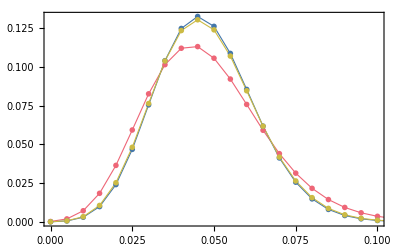

```mathematica
myfontsize=15;pad=35;padding={{pad,pad},{Auto,Auto}};pms=14;plotr1a=ListPlot[{T@{ran/ni,qqx},T@{ran/ni,qqmar},T@{ran/ni,qqmix}},Joined->True,PlotRange->{{0,0.1},All},
Joined->True,Axes->False,Frame->{True,True,False,False},FrameLabel->None(*myaxes[{OverBar[r],HoldForm[Style[P,Plain][OverBar[x] == OverBar[r]"|" Style[Ι,Italic]]]}]*),PlotStyle->{{Opacity[1],red,Thickness[0.002]},{Opacity[1],purpleblue,Thickness[0.002]}, {Opacity[1],yellow,Thickness[0.002]}},PlotMarkers->{{emptySquare,pms},{emptyUpTriangle,pms},{emptyCircle,pms}},(*PlotLegends->mylegends[{"maxent at population level, marginalized","maxent at sample level"},Top],*)PlotTheme->{"OpenMarkersThick"},FrameTicks->Auto(*{Auto,
(*Table[{10^i,Superscript[10,i],{.02,0}},{i,-60,10,10}]~Join~Flatten[Table[{j 10^i, ,{.005,0}},{i,-60,10,10},{j,200,900,100}],1]*)
Table[{10^i,If[i==0,1,Superscript[10,i]]},{i,-60,10,20}]
,None,None}*),AspectRatio->1/GoldenRatio,ImagePadding->padding]
```

```mathematica
myfontsize=15;pad=35;padding={{pad,pad},{Auto,Auto}};pms=14;plotr1a=ListPlot[{T@{ran/ni,qqx},T@{ran/ni,qqmar},T@{ran/ni,qqmix}},Joined->True,PlotRange->{{0,0.1},All},
Joined->True,Axes->False,Frame->{True,True,False,False},myframestyle,FrameLabel->None(*myaxes[{OverBar[r],HoldForm[Style[P,Plain][OverBar[x] == OverBar[r]"|" Style[Ι,Italic]]]}]*),PlotStyle->{{Opacity[1],red,Thickness[0.002]},{Opacity[1],purpleblue,Thickness[0.002]}, {Opacity[1],yellow,Thickness[0.002]}},PlotMarkers->{{emptySquare,pms},{emptyUpTriangle,pms},{emptyCircle,pms}},(*PlotLegends->mylegends[{"maxent at population level, marginalized","maxent at sample level"},Top],*)PlotTheme->{"OpenMarkersThick"},FrameTicks->Auto(*{Auto,
(*Table[{10^i,Superscript[10,i],{.02,0}},{i,-60,10,10}]~Join~Flatten[Table[{j 10^i, ,{.005,0}},{i,-60,10,10},{j,200,900,100}],1]*)
Table[{10^i,If[i==0,1,Superscript[10,i]]},{i,-60,10,20}]
,None,None}*),AspectRatio->1/GoldenRatio,ImagePadding->padding]
```

-Graphics-

```mathematica
myfontsize=16;
opac=0.75;pad=75;padding={{pad,Auto},{Auto,Auto}};pms=10;plotr1=ListPlot[{T@{ran/ni,qqx},T@{ran/ni,qqmar},T@{ran/ni,qqmix}},Joined->True,PlotRange->{{0,1},All},
Joined->True,Axes->False,Frame->{False,True,False,False},myframestyle,FrameLabel->myaxes[{OverBar[r],HoldForm[Style[P,Plain][OverBar[S] == OverBar[s](*"|" Style[Ι,Italic]*)]]}],PlotStyle->{{Opacity[opac],red,Thickness[0.002]},{Opacity[opac],purpleblue,Thickness[0.002]}, {Opacity[opac],yellow,Thickness[0.002]}},PlotMarkers->{{emptySquare,pms},{emptyUpTriangle,pms},{emptyCircle,pms}},PlotLegends->mylegends[{"sample level","pop. level","unknown pop. level"},Top],PlotTheme->{"OpenMarkersThick"},FrameTicks->Auto(*{Auto,
(*Table[{10^i,Superscript[10,i],{.02,0}},{i,-60,10,10}]~Join~Flatten[Table[{j 10^i, ,{.005,0}},{i,-60,10,10},{j,200,900,100}],1]*)
Table[{10^i,If[i==0,1,Superscript[10,i]]},{i,-60,10,20}]
,None,None}*),AspectRatio->1/(1.75*GoldenRatio),ImagePadding->padding,Epilog->Inset[plotr1a,Scaled[{3/5,1}],{Center,Top},{0.6,Auto}]]
```

-Graphics-

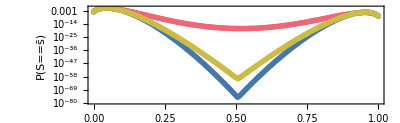

```mathematica
opac=0.75;pms=10;plotr2=ListLogPlot[{T@{ran/ni,qqx},T@{ran/ni,qqmar},T@{ran/ni,qqmix}},Joined->True,PlotRange->{{0,1},All},
Joined->True,Axes->False,Frame->{True,True,False,False},myframestyle,FrameLabel->myaxes[{OverBar[s],HoldForm[Style[P,Plain][OverBar[S] == OverBar[s](*"|" Style[Ι,Italic]*)]]}],PlotStyle->{{Opacity[opac],red,Thickness[0.002]}, {Opacity[opac],purpleblue,Thickness[0.002]}, {Opacity[opac],yellow,Thickness[0.002]}},PlotMarkers->{{emptySquare,pms},{emptyUpTriangle,pms},{emptyCircle,pms}},(*PlotLegends->mylegends[{"maxent at population level, marginalized","maxent at sample level"},Top],*)PlotTheme->{"OpenMarkersThick"},FrameTicks->Auto(*{Auto,
(*Table[{10^i,Superscript[10,i],{.02,0}},{i,-60,10,10}]~Join~Flatten[Table[{j 10^i, ,{.005,0}},{i,-60,10,10},{j,200,900,100}],1]*)
Table[{10^i,If[i==0,1,Superscript[10,i]]},{i,-60,10,20}]
,None,None}*),AspectRatio->1/(2*GoldenRatio),ImagePadding->padding]
```

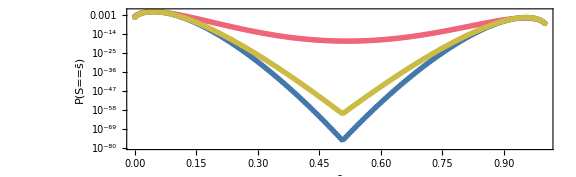
-Graphics-
-Graphics-

```mathematica
Grid[{{show@plotr1},{show@plotr2}},Spacings->Auto]
```

```mathematica
expdf0r["comparison3"]
```

comparison3.pdf

```mathematica
nn=5000;rann=(Range[0,nn]/nn);
```

```mathematica
a1=0.45;a2=0.35;
```

```mathematica
(* calculate Lagr multipliers with two methods and compare results *)
```

```mathematica
{zj1,zj2,qq2,norm2}=MEhomsolution2[a1,a2,nn,30][[1;;4]];
```

```mathematica
{zj1,zj2,qq2b,norm2}=MEhomsolution[a1,a2,nn,30][[1;;4]];
```

```mathematica
{zj1*nn,zj2*nn*(nn-1)/2,norm2}
```

{-6.66093365513262187960208393633×10^7,1.66485848046995830741504115398×10^11,2.335550732575446583112822×10^186}

```mathematica
ListLogPlot[{T@{rann,qq2*nn},T@{rann,qq2b*nn}}, Joined->True,PlotRange->All]
```

```mathematica
(* Marginalize max-entropy distribution at population level to subpopulation of 100 units. Done by multiplying for hypergeometric distribution *)
ni=100;qqmar=Block[{list=Table[condp[ni,r,nn,rr],{r,0,ni},{rr,0,nn}].qq2},list/Total[list]];
```

```mathematica
ran=(Range[0,ni]/ni);ListLogPlot[{T@{ran,qqmar*ni},T@{rann,qq2*nn}}, Joined->True]
```

```mathematica
(* maximum-entropy distr. calculated directly at subpopulation level *)
{zj1,zj2,qqx}=MEhomsolution[a1,a2,ni,60][[1;;3]];
```

```mathematica
{zj1*ni,zj2*ni*(ni-1)/2}
```

{-26928.0062502814685306734038105732530242863762264980947549572,1.33128756574084917055328210394113172341406658369139500731702×10^6}

```mathematica
ListLogPlot[{T@{ran,qqx*ni},T@{ran,qqmar*ni}}, Joined->True,PlotStyle->{{blue,Dashed,Thick},red}]
```

```mathematica
ListPlot[{T@{ran,qqx*ni},T@{ran,qqmar*ni}}, Joined->True,PlotStyle->{{blue,Dashed,Thick},red},PlotRange->All]
```

```mathematica
pms=14;ListPlot[{T@{ran,qqmar},T@{ran,qqx}},Joined->True,PlotRange->All,
Joined->True,Axes->False,Frame->{True,True,False,False},myframestyle,FrameLabel->myaxes[{OverBar[r],HoldForm[Style[P,Plain][OverBar[x] == OverBar[r]"|" Style[Ι,Italic]]]}],PlotStyle->{{Opacity[1],blue,Thickness[0.002]}, {Opacity[1],red,Thickness[0.002]}},PlotMarkers->{{emptyUpTriangle,pms},{emptyCircle,pms}},PlotRange->All,PlotLegends->mylegends[{"maxent at population level, marginalized","maxent at sample level"},Top],PlotTheme->{"OpenMarkersThick"},FrameTicks->Auto(*{Auto,
(*Table[{10^i,Superscript[10,i],{.02,0}},{i,-60,10,10}]~Join~Flatten[Table[{j 10^i, ,{.005,0}},{i,-60,10,10},{j,200,900,100}],1]*)
Table[{10^i,If[i==0,1,Superscript[10,i]]},{i,-60,10,20}]
,None,None}*),AspectRatio->GoldenRatio]
```

```mathematica
expdf["different_maxent_pop_sample_100_h"]
```

../work/different_maxent_pop_sample_100_h.pdf

```mathematica
pms=14;ListLogPlot[{T@{ran,qqmar},T@{ran,qqx}},Joined->True,PlotRange->All,
Joined->True,Axes->False,Frame->{True,True,False,False},myframestyle,FrameLabel->myaxes[{OverBar[r],HoldForm[Style[P,Plain][OverBar[x] == OverBar[r]"|" Style[Ι,Italic]]]}],PlotStyle->{{Opacity[1],blue,Thickness[0.002]}, {Opacity[1],red,Thickness[0.002]}},PlotMarkers->{{emptyUpTriangle,pms},{emptyCircle,pms}},PlotRange->All,PlotLegends->mylegends[{"maxent at population level, marginalized","maxent at sample level"},Top],PlotTheme->{"OpenMarkersThick"},FrameTicks->Auto(*{Auto,
(*Table[{10^i,Superscript[10,i],{.02,0}},{i,-60,10,10}]~Join~Flatten[Table[{j 10^i, ,{.005,0}},{i,-60,10,10},{j,200,900,100}],1]*)
Table[{10^i,If[i==0,1,Superscript[10,i]]},{i,-60,10,20}]
,None,None}*),AspectRatio->1/GoldenRatio]
```

```mathematica
expdf["different_maxent_pop_sample_100_log"]
```

../work/different_maxent_pop_sample_100_log.pdf

```mathematica
ran.qqmar
```

0.45

```mathematica
(ran*(ni*ran-1)/(ni-1)).qqmar
```

0.35

```mathematica
ran.qqx
```

0.450000000000000011102230246251565404236316680908203125

```mathematica
(ran*(ni*ran-1)/(ni-1)).qqx
```

0.34999999999999997779553950749686919152736663818359375

```mathematica
ne=3;qm1=Block[{list=Table[condp[ne,r,nn,rr],{r,0,ne},{rr,0,nn}].qq2},list/Total[list]]
```

{0.395007,0.16498,0.135019,0.304994}

```mathematica
qm1e=Block[{list=Table[condp[ne,r,ni,rr],{r,0,ne},{rr,0,ni}].qqx},list/Total[list]]
```

{0.395349,0.163954,0.136046,0.304651}

```mathematica
a1=0.045;a2=0.0025;
```

```mathematica
{zj1,zj2,qq2,norm2}=MEhomsolution[a1,a2,nn,30][[1;;4]];
```

```mathematica
{zj1*nn,zj2*nn*(nn-1)/2,norm2}
```

{-16834.0241314757191953174975757,16825.7341457796331938241265183,2.15424488636136194849991231×10^84}

```mathematica
ListLogPlot[T@{rann,qq2*nn}, Joined->True,PlotRange->All]
```

```mathematica
ni=200;qqmar=Block[{list=Table[condp[ni,r,nn,rr],{r,0,ni},{rr,0,nn}].qq2},list/Total[list]];
```

```mathematica
ran=(Range[0,ni]/ni);ListLogPlot[{T@{ran,qqmar*ni},T@{rann,qq2*nn}}, Joined->True]
```

```mathematica
{zj1,zj2,qqx,normx}=MEhomsolution[a1,a2,ni,60][[1;;4]];
```

```mathematica
{zj1*ni,zj2*ni*(ni-1)/2,normx}
```

{-673.531437143944906695367530315732752209110380368572698028302,665.075941496378957769164409996988495715814939058691175007534,2365.841055127091219513264300359750485427830365462726921698}

```mathematica
ListLogPlot[{T@{ran,qqx*ni},T@{ran,qqmar*ni}}, Joined->True,PlotStyle->{{blue,Dashed,Thick},red}]
```

```mathematica
ListPlot[{T@{ran,qqx*ni},T@{ran,qqmar*ni}}, Joined->True,PlotStyle->{{blue,Dashed,Thick},red},PlotRange->All]
```

```mathematica
sidesquare=2*Sqrt[3]*3/8
```

(3 √3)/4

```mathematica
radiuscircle=Sqrt[(2*Sqrt[3]*3/2)/Pi];
```

```mathematica
radiuscircle=2*Sqrt[3]*3/(2*Pi);
```

```mathematica
size=2;absoluteThickness=1;
emptySquare=Graphics[{AbsoluteThickness[absoluteThickness],JoinedCurve[Line[{Offset[size {sidesquare,sidesquare}],Offset[size {-sidesquare,sidesquare}],Offset[size {-sidesquare,-sidesquare}],Offset[size {sidesquare,-sidesquare}]}],CurveClosed->True]},AlignmentPoint->{0,0}];
emptyUpTriangle=Graphics[{AbsoluteThickness[absoluteThickness],JoinedCurve[Line[{Offset[size {0,2}],Offset[size {Sqrt[3],-1}],Offset[size {-Sqrt[3],-1}]}],CurveClosed->True]},AlignmentPoint->{0,0}];
filledUpTriangle=Graphics[{Triangle[{Offset[size {0,2}+absoluteThickness {0,1}],Offset[size {Sqrt[3],-1}+absoluteThickness {Sqrt[3/4],-1/2}],Offset[size {-Sqrt[3],-1}+absoluteThickness {-Sqrt[3/4],-1/2}]}]},AlignmentPoint->{0,0}];
{emptyLeftTriangle,filledLeftTriangle,emptyDownTriangle,filledDownTriangle,emptyRightTriangle,filledRightTriangle}=Flatten[{emptyUpTriangle,filledUpTriangle}/.{x_?NumericQ,y_?NumericQ}:>RotationTransform[#][{x,y}]&/@{Pi/2,Pi/3,-Pi/2}];
emptyCircle=Graphics[{AbsoluteThickness[absoluteThickness],Circle[{0,0},Offset[size*radiuscircle+absoluteThickness]]},AlignmentPoint->{0,0}];
```

```mathematica
pad=50;padding={{pad,pad},{Auto,Auto}}
```

{{50,50},{Automatic,Automatic}}

```mathematica
pms=14;plotr1=ListPlot[{T@{ran,qqmar},T@{ran,qqx}},Joined->True,PlotRange->{{0,1},All},
Joined->True,Axes->False,Frame->{False,True,False,False},myframestyle,FrameLabel->myaxes[{OverBar[r],HoldForm[Style[P,Plain][OverBar[x] == OverBar[r]"|" Style[Ι,Italic]]]}],PlotStyle->{{Opacity[1],blue,Thickness[0.002]}, {Opacity[1],red,Thickness[0.002]}},PlotMarkers->{{emptyUpTriangle,pms},{emptyCircle,pms}},PlotLegends->mylegends[{"maxent at population level, marginalized","maxent at sample level"},Top],PlotTheme->{"OpenMarkersThick"},FrameTicks->Auto(*{Auto,
(*Table[{10^i,Superscript[10,i],{.02,0}},{i,-60,10,10}]~Join~Flatten[Table[{j 10^i, ,{.005,0}},{i,-60,10,10},{j,200,900,100}],1]*)
Table[{10^i,If[i==0,1,Superscript[10,i]]},{i,-60,10,20}]
,None,None}*),AspectRatio->1/GoldenRatio,ImagePadding->padding]
```

```mathematica
expdf["different_maxent_pop_sample_200_realdata"]
```

../work/different_maxent_pop_sample_200_realdata.pdf

```mathematica
pms=14;plotr2=ListLogPlot[{T@{ran,qqmar},T@{ran,qqx}},Joined->True,PlotRange->{{0,1},All},
Joined->True,Axes->False,Frame->{True,True,False,False},myframestyle,FrameLabel->myaxes[{OverBar[r],HoldForm[Style[P,Plain][OverBar[x] == OverBar[r]"|" Style[Ι,Italic]]]}],PlotStyle->{{Opacity[1],blue,Thickness[0.002]}, {Opacity[1],red,Thickness[0.002]}},PlotMarkers->{{emptyUpTriangle,pms},{emptyCircle,pms}},(*PlotLegends->mylegends[{"maxent at population level, marginalized","maxent at sample level"},Top],*)PlotTheme->{"OpenMarkersThick"},FrameTicks->Auto(*{Auto,
(*Table[{10^i,Superscript[10,i],{.02,0}},{i,-60,10,10}]~Join~Flatten[Table[{j 10^i, ,{.005,0}},{i,-60,10,10},{j,200,900,100}],1]*)
Table[{10^i,If[i==0,1,Superscript[10,i]]},{i,-60,10,20}]
,None,None}*),AspectRatio->1/GoldenRatio,ImagePadding->padding]
```

```mathematica
expdf["different_maxent_pop_sample_200_realdata_log"]
```

../work/different_maxent_pop_sample_200_realdata_log.pdf

```mathematica
Grid[{{plotr1},{plotr2}}]
```

```mathematica
expdf["different_maxent_pop_sample_200_realdata_both"]
```

../work/different_maxent_pop_sample_200_realdata_both.pdf

```mathematica
(* With four moments *)
```

```mathematica
popact=Round[Flatten[Import["popact_SANA_bin3.npy","Table"]]]
```

```mathematica
Length[popact]
```

300394

```mathematica
prod[2]//N
```

0.00261369

```mathematica
Mean[(popact^2-popact)]/(num^2-num)//N
```

0.00261369

```mathematica
num=159;
```

```mathematica
prod[r_]:=prod[r]=(Mean[Binomial[popact,r]/Binomial[num,r]])
```

```mathematica
Array[prod,4]//N
```

{0.0498669,0.00261369,0.000145633,8.76024×10^-6}

```mathematica
N[{a1=prod[1],a2=prod[2],a3=prod[3], a4=prod[4]},3]
```

{0.0499,0.00261,0.000146,8.76×10^-6}

```mathematica
N[Array[prod,4],3]
```

{0.0499,0.00261,0.000146,8.76×10^-6}

```mathematica
N[{a1,a2,a3,a4}={478/10000,257/100000,148/1000000,881/100000000},3]
```

{0.0478,0.00257,0.000148,8.81×10^-6}

```mathematica
nn=5000;rann=Range[0,nn];
```

```mathematica
<<"scripts/ME_4momsolution2.m"
```

```mathematica
<<"scripts/ME_4momsolution.m"
```

```mathematica
<<"scripts/ME_4momsolution3.m"
```

```mathematica
{zj1,zj2,zj3,zj4,qq2c,norm2}=MEhom4moments3[a1,a2,a3,a4,nn,60];
```

```mathematica
{zj1,zj2,zj3,zj4,qq2b,norm2}=MEhom4moments2[a1,a2,a3,a4,nn,60];
```

```mathematica
{zj1,zj2,zj3,zj4,qq2,norm2}=MEhom4moments2[a1,a2,a3,a4,nn,60];
```

```mathematica
{{a1,a2,a3,a4},Table[(Binomial[rann,i].qq2)/Binomial[nn,i],{i,4}]}//T//MF//N
```

(0.0478 | 0.0529512
0.00257 | 0.00279397
0.000148 | 0.000146903
8.81×10^-6 | 7.69656×10^-6)

```mathematica
{aa1,aa2,aa3,aa4}=Table[(Binomial[rann,i].qq2)/Binomial[nn,i],{i,4}]
```

{0.05295118915212402146658572698058091128110645606210516774,0.002793965353542041758594173517114705722907785679730701525,0.000146902762168926338692482748482437529305967219791822154,7.696558527153208748657138713411391630138232826779200564×10^-6}

```mathematica
ni=200;ran=Range[0,ni];qqmar=Block[{list=Table[condp[ni,r,nn,rr],{r,0,ni},{rr,0,nn}].qq2},list/Total[list]];
```

```mathematica
ListLogPlot[{T@{ran/ni,qqmar*ni},T@{rann/nn,qq2*nn}}, Joined->True,PlotRange->All]
```

```mathematica
{zj1,zj2,zj3,zj4,qqx,normx}=MEhom4moments2[aa1,aa2,aa3,aa4,ni,60];
```

```mathematica
{{aa1,aa2,aa3,aa4},Table[(Binomial[ran,i].qqx)/Binomial[ni,i],{i,4}]}//T//MF//N
```

(0.0526517 | 0.0526517
0.00276239 | 0.00276239
0.000144415 | 0.000144415
7.52296×10^-6 | 7.52296×10^-6)

```mathematica
nn=1000;rann=Range[0,nn];
```

```mathematica
{zj1,zj2,zj3,zj4,qq2bis,norm2}=MEhom4moments2[aa1,aa2,aa3,aa4,nn,60];
```

```mathematica
{{aa1,aa2,aa3,aa4},Table[(Binomial[rann,i].qq2bis)/Binomial[nn,i],{i,4}]}//T//MF//N
```

(0.0526517 | 0.0526308
0.00276239 | 0.00275959
0.000144415 | 0.000144217
7.52296×10^-6 | 7.51615×10^-6)

```mathematica
{zj1*ni,zj2*ni*(ni-1)/2,normx}
```

{-673.531437143944906695367530315732752209110380368572698028302,665.075941496378957769164409996988495715814939058691175007534,2365.841055127091219513264300359750485427830365462726921698}

```mathematica
ListPlot[{T@{ran,qqx*ni},T@{ran,qqmar*ni}}, Joined->True,PlotStyle->{{blue,Dashed,Thick},red},PlotRange->All]
```

```mathematica
myfontsize=18;
```

```mathematica
sidesquare=2*Sqrt[3]*3/8;radiuscircle=Sqrt[(2*Sqrt[3]*3/2)/Pi];
(*radiuscircle=2*Sqrt[3]*3/(2*Pi);*)

size=2;absoluteThickness=1;
emptySquare=Graphics[{AbsoluteThickness[absoluteThickness],JoinedCurve[Line[{Offset[size {sidesquare,sidesquare}],Offset[size {-sidesquare,sidesquare}],Offset[size {-sidesquare,-sidesquare}],Offset[size {sidesquare,-sidesquare}]}],CurveClosed->True]},AlignmentPoint->{0,0}];
emptyUpTriangle=Graphics[{AbsoluteThickness[absoluteThickness],JoinedCurve[Line[{Offset[size {0,2}],Offset[size {Sqrt[3],-1}],Offset[size {-Sqrt[3],-1}]}],CurveClosed->True]},AlignmentPoint->{0,0}];
filledUpTriangle=Graphics[{Triangle[{Offset[size {0,2}+absoluteThickness {0,1}],Offset[size {Sqrt[3],-1}+absoluteThickness {Sqrt[3/4],-1/2}],Offset[size {-Sqrt[3],-1}+absoluteThickness {-Sqrt[3/4],-1/2}]}]},AlignmentPoint->{0,0}];
{emptyLeftTriangle,filledLeftTriangle,emptyDownTriangle,filledDownTriangle,emptyRightTriangle,filledRightTriangle}=Flatten[{emptyUpTriangle,filledUpTriangle}/.{x_?NumericQ,y_?NumericQ}:>RotationTransform[#][{x,y}]&/@{Pi/2,Pi/3,-Pi/2}];
emptyCircle=Graphics[{AbsoluteThickness[absoluteThickness],Circle[{0,0},Offset[size*radiuscircle+absoluteThickness]]},AlignmentPoint->{0,0}];
```

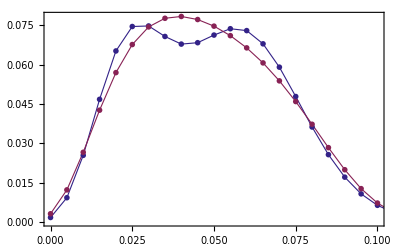

```mathematica
myfontsize=15;pad=35;padding={{pad,pad},{Auto,Auto}};pms=14;plotr1a=ListPlot[{T@{ran/ni,qqmar},T@{ran/ni,qqx}},Joined->True,PlotRange->{{0,0.1},All},
Joined->True,Axes->False,Frame->{True,True,False,False},myframestyle,FrameLabel->None(*myaxes[{OverBar[r],HoldForm[Style[P,Plain][OverBar[x] == OverBar[r]"|" Style[Ι,Italic]]]}]*),PlotStyle->{{Opacity[1],blue,Thickness[0.002]}, {Opacity[1],red,Thickness[0.002]}},PlotMarkers->{{emptyUpTriangle,pms},{emptyCircle,pms}},(*PlotLegends->mylegends[{"maxent at population level, marginalized","maxent at sample level"},Top],*)PlotTheme->{"OpenMarkersThick"},FrameTicks->Auto(*{Auto,
(*Table[{10^i,Superscript[10,i],{.02,0}},{i,-60,10,10}]~Join~Flatten[Table[{j 10^i, ,{.005,0}},{i,-60,10,10},{j,200,900,100}],1]*)
Table[{10^i,If[i==0,1,Superscript[10,i]]},{i,-60,10,20}]
,None,None}*),AspectRatio->1/GoldenRatio,ImagePadding->padding]
```

```mathematica
ratio=Sqrt[2];
```

```mathematica
myfontsize=18;pad=75;padding={{pad,Auto},{Auto,Auto}};pms=14;plotr1=ListPlot[{T@{ran/ni,qqmar},T@{ran/ni,qqx}},Joined->True,PlotRange->{{0,1},All},
Joined->True,Axes->False,Frame->{False,True,False,False},myframestyle,FrameLabel->myaxes[{OverBar[r],HoldForm[Style[P,Plain][OverBar[x] == OverBar[r](*"|" Style[Ι,Italic]*)]]}],PlotStyle->{{Opacity[1],blue,Thickness[0.002]}, {Opacity[1],red,Thickness[0.002]}},PlotMarkers->{{emptyUpTriangle,pms},{emptyCircle,pms}},PlotLegends->mylegends[{"maxent at population level, marginalized","maxent at sample level"},Top],PlotTheme->{"OpenMarkersThick"},FrameTicks->Auto(*{Auto,
(*Table[{10^i,Superscript[10,i],{.02,0}},{i,-60,10,10}]~Join~Flatten[Table[{j 10^i, ,{.005,0}},{i,-60,10,10},{j,200,900,100}],1]*)
Table[{10^i,If[i==0,1,Superscript[10,i]]},{i,-60,10,20}]
,None,None}*),AspectRatio->1/GoldenRatio,ImagePadding->padding,Epilog->Inset[plotr1a,Scaled[{2/3,1}],{Center,Top},{0.7,Auto}]]
```

-Graphics-

```mathematica
expdf["different_maxent_pop_sample_200_realdata"]
```

../work/different_maxent_pop_sample_200_realdata.pdf

```mathematica
pms=14;plotr2=ListLogPlot[{T@{ran/ni,qqmar},T@{ran/ni,qqx}},Joined->True,PlotRange->{{0,1},{10^-260,1}},
Joined->True,Axes->False,Frame->{True,True,False,False},myframestyle,FrameLabel->myaxes[{OverBar[r],HoldForm[Style[P,Plain][OverBar[x] == OverBar[r](*"|" Style[Ι,Italic]*)]]}],PlotStyle->{{Opacity[1],blue,Thickness[0.002]}, {Opacity[1],red,Thickness[0.002]}},PlotMarkers->{{emptyUpTriangle,pms},{emptyCircle,pms}},(*PlotLegends->mylegends[{"maxent at population level, marginalized","maxent at sample level"},Top],*)PlotTheme->{"OpenMarkersThick"},FrameTicks->Auto(*{Auto,
(*Table[{10^i,Superscript[10,i],{.02,0}},{i,-60,10,10}]~Join~Flatten[Table[{j 10^i, ,{.005,0}},{i,-60,10,10},{j,200,900,100}],1]*)
Table[{10^i,If[i==0,1,Superscript[10,i]]},{i,-60,10,20}]
,None,None}*),AspectRatio->1/(2*GoldenRatio),ImagePadding->padding]
```

```mathematica
expdf["different_maxent_pop_sample_200_realdata_log"]
```

../work/different_maxent_pop_sample_200_realdata_log.pdf

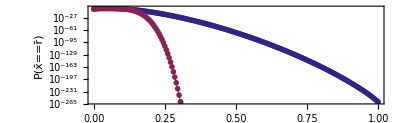
-Graphics-
-Graphics-

```mathematica
Grid[{{plotr1},{plotr2}}]
```

```mathematica
expdf["different_maxent_pop_sample_200_realdata_4mom"]
```

../work/different_maxent_pop_sample_200_realdata_4mom.pdf

```mathematica
N[{aa1,aa2,aa3,aa4},3]
```

{0.0478,0.00257,0.000148,8.81×10^-6}

```mathematica
qqmarold=qqmar;qqxold=qqx;qq2old=qq2;
```

```mathematica
(* With two moments *)
```

```mathematica
popact=Round[Flatten[Import["C:\\Users\\pglpm\\work\\popact_SANA_bin3.npy","Table"]]];
```

```mathematica
Length[popact]
```

300394

```mathematica
prod[2]//N
```

0.00261369

```mathematica
Mean[(popact^2-popact)]/(num^2-num)//N
```

0.00261369

```mathematica
num=159;
```

```mathematica
prod[r_]:=prod[r]=(Mean[Binomial[popact,r]/Binomial[num,r]])
```

```mathematica
Array[prod,4]//N
```

{0.0498669,0.00261369,0.000145633,8.76024×10^-6}

```mathematica
a1=prod[1];a2=prod[2];a3=prod[3]; a4=prod[4];
```

```mathematica
N[Array[prod,4],3]
```

{0.0499,0.00261,0.000146,8.76×10^-6}

```mathematica
({a1,a2,a3,a4}={5*10^-2,26*10^-4,15 *10^-5,88*10^-7})//N
```

{0.05,0.0026,0.00015,8.8×10^-6}

```mathematica
N[{aa1,aa2,aa3,aa4}={478/10000,257/100000,148/1000000,881/100000000},3]
```

{0.0478,0.00257,0.000148,8.81×10^-6}

```mathematica
nn=5000;rann=Range[0,nn];
```

```mathematica
<<($HomeDirectory<>"/work/scripts/ME_homsolution.m")
```

```mathematica
{zj1,zj2,zj3,zj4,qq2c,norm2}=MEhom4moments3[a1,a2,a3,a4,nn,60];
```

```mathematica
{zj1,zj2,qq2b,norm2}=MEhom4moments2[a1,a2,a3,a4,nn,60];
```

```mathematica
{zj1,zj2,qq2,norm2}=MEhomsolution[aa1,aa2,nn,60];
```

```mathematica
{{aa1,aa2,aa3,aa4},Table[(Binomial[rann,i].qq2)/Binomial[nn,i],{i,4}]}//T//MF//N
```

(0.0478 | 0.0478
0.00257 | 0.00257
0.000148 | 0.000404437
8.81×10^-6 | 0.0002878)

```mathematica
{aa1,aa2,aa3,aa4}=Table[(Binomial[rann,i].qq2)/Binomial[nn,i],{i,4}]
```

{0.047799999999999999999999999997566331411840104937154229139,0.0025699999999999999999999999976746655087610553804674786181,0.0004044371898436149006057451137842255212624918472549544123,0.0002878002780004204029882525717306820440828143747701507318}

```mathematica
ni=200;ran=Range[0,ni];qqmar=Block[{list=Table[condp[ni,r,nn,rr],{r,0,ni},{rr,0,nn}].qq2},list/Total[list]];
```

```mathematica
ListPlot[{T@{ran/ni,qqmar*ni},T@{rann/nn,qq2*nn}}, Joined->True,PlotRange->All]
```

```mathematica
{zj1,zj2,qqx,normx}=MEhomsolution[aa1,aa2,ni,60];
```

```mathematica
{{aa1,aa2},Table[(Binomial[ran,i].qqx)/Binomial[ni,i],{i,2}]}//T//MF//N
```

(0.0478 | 0.0478
0.00257 | 0.00257)

```mathematica
Clear[qq2bis];
Table[rann=Range[0,nn2];qq2bis[nn2]=MEhomsolution[aa1,aa2,nn2,60][[3]];{{aa1,aa2},Table[(Binomial[rann,i].qq2bis[nn2])/Binomial[nn2,i],{i,2}]}//T//MF//N,{nn2,{5000,10000,10^6}}]
```

```mathematica
ListLogPlot[Table[T@{Range[0,nn2]/nn2,qq2bis[nn2]*nn2},{nn2,{5000,10000,10^6}}]]
```

```mathematica
nn=1000;rann=Range[0,nn];
```

```mathematica
{zj1,zj2,qq2bis,norm2}=MEhomsolution[aa1,aa2,nn,60];
```

```mathematica
{{aa1,aa2,aa3,aa4},Table[(Binomial[rann,i].qq2bis)/Binomial[nn,i],{i,4}]}//T//MF//N
```

(0.0478 | 0.0478
0.00257 | 0.00257
0.000148 | 0.000390116
8.81×10^-6 | 0.000271883)

```mathematica
ni=200;ran=Range[0,ni];qqmarbis=Block[{list=Table[condp[ni,r,nn,rr],{r,0,ni},{rr,0,nn}].qq2bis},list/Total[list]];
```

```mathematica
ListLogPlot[{T@{ran/ni,qqmar*ni},T@{Range[0,5000]/5000,qq2*5000},T@{ran/ni,qqmarbis*ni},T@{rann/nn,qq2bis*nn}}, Joined->True,PlotRange->All,PlotStyle->{Auto,Auto,Dashed,Dashed}]
```

```mathematica
ListPlot[{T@{ran/ni,qqx*ni},T@{ran/ni,qqmar*ni}}, Joined->True,PlotStyle->{{blue,Dashed,Thick},red},PlotRange->All]
```

```mathematica
sidesquare=2*Sqrt[3]*3/8;radiuscircle=Sqrt[(2*Sqrt[3]*3/2)/Pi];
(*radiuscircle=2*Sqrt[3]*3/(2*Pi);*)

size=2;absoluteThickness=1;
emptySquare=Graphics[{AbsoluteThickness[absoluteThickness],JoinedCurve[Line[{Offset[size {sidesquare,sidesquare}],Offset[size {-sidesquare,sidesquare}],Offset[size {-sidesquare,-sidesquare}],Offset[size {sidesquare,-sidesquare}]}],CurveClosed->True]},AlignmentPoint->{0,0}];
emptyUpTriangle=Graphics[{AbsoluteThickness[absoluteThickness],JoinedCurve[Line[{Offset[size {0,2}],Offset[size {Sqrt[3],-1}],Offset[size {-Sqrt[3],-1}]}],CurveClosed->True]},AlignmentPoint->{0,0}];
filledUpTriangle=Graphics[{Triangle[{Offset[size {0,2}+absoluteThickness {0,1}],Offset[size {Sqrt[3],-1}+absoluteThickness {Sqrt[3/4],-1/2}],Offset[size {-Sqrt[3],-1}+absoluteThickness {-Sqrt[3/4],-1/2}]}]},AlignmentPoint->{0,0}];
{emptyLeftTriangle,filledLeftTriangle,emptyDownTriangle,filledDownTriangle,emptyRightTriangle,filledRightTriangle}=Flatten[{emptyUpTriangle,filledUpTriangle}/.{x_?NumericQ,y_?NumericQ}:>RotationTransform[#][{x,y}]&/@{Pi/2,Pi/3,-Pi/2}];
emptyCircle=Graphics[{AbsoluteThickness[absoluteThickness],Circle[{0,0},Offset[size*radiuscircle+absoluteThickness]]},AlignmentPoint->{0,0}];
```

```mathematica
myfontsize=15;pad=35;padding={{pad,pad},{Auto,Auto}};pms=14;plotr1a=ListPlot[{T@{ran/ni,qqmar},T@{ran/ni,qqx}},Joined->True,PlotRange->{{0,0.1},All},
Joined->True,Axes->False,Frame->{True,True,False,False},myframestyle,FrameLabel->None(*myaxes[{OverBar[r],HoldForm[Style[P,Plain][OverBar[x] == OverBar[r]"|" Style[Ι,Italic]]]}]*),PlotStyle->{{Opacity[1],blue,Thickness[0.002]}, {Opacity[1],red,Thickness[0.002]}},PlotMarkers->{{emptyUpTriangle,pms},{emptyCircle,pms}},(*PlotLegends->mylegends[{"maxent at population level, marginalized","maxent at sample level"},Top],*)PlotTheme->{"OpenMarkersThick"},FrameTicks->Auto(*{Auto,
(*Table[{10^i,Superscript[10,i],{.02,0}},{i,-60,10,10}]~Join~Flatten[Table[{j 10^i, ,{.005,0}},{i,-60,10,10},{j,200,900,100}],1]*)
Table[{10^i,If[i==0,1,Superscript[10,i]]},{i,-60,10,20}]
,None,None}*),AspectRatio->1/GoldenRatio,ImagePadding->padding]
```

```mathematica
myfontsize=18;pad=75;padding={{pad,Auto},{Auto,Auto}};pms=14;plotr1=ListPlot[{T@{ran/ni,qqmar},T@{ran/ni,qqx}},Joined->True,PlotRange->{{0,1},All},
Joined->True,Axes->False,Frame->{False,True,False,False},myframestyle,FrameLabel->myaxes[{OverBar[r],HoldForm[Style[P,Plain][OverBar[x] == OverBar[r](*"|" Style[Ι,Italic]*)]]}],PlotStyle->{{Opacity[1],blue,Thickness[0.002]}, {Opacity[1],red,Thickness[0.002]}},PlotMarkers->{{emptyUpTriangle,pms},{emptyCircle,pms}},PlotLegends->mylegends[{"maxent at population level, marginalized","maxent at sample level"},Top],PlotTheme->{"OpenMarkersThick"},FrameTicks->Auto(*{Auto,
(*Table[{10^i,Superscript[10,i],{.02,0}},{i,-60,10,10}]~Join~Flatten[Table[{j 10^i, ,{.005,0}},{i,-60,10,10},{j,200,900,100}],1]*)
Table[{10^i,If[i==0,1,Superscript[10,i]]},{i,-60,10,20}]
,None,None}*),AspectRatio->1/GoldenRatio,ImagePadding->padding,Epilog->Inset[plotr1a,Scaled[{2/3,1}],{Center,Top},{0.7,Auto}]]
```

-Graphics-

```mathematica
expdf["different_maxent_pop_sample_200_realdata"]
```

../work/different_maxent_pop_sample_200_realdata.pdf

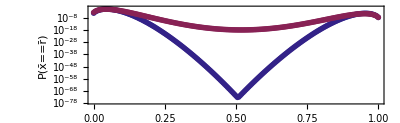

```mathematica
pms=14;plotr2=ListLogPlot[{T@{ran/ni,qqmar},T@{ran/ni,qqx}},Joined->True,PlotRange->{{0,1},{All,1}},
Joined->True,Axes->False,Frame->{True,True,False,False},myframestyle,FrameLabel->myaxes[{OverBar[r],HoldForm[Style[P,Plain][OverBar[x] == OverBar[r](*"|" Style[Ι,Italic]*)]]}],PlotStyle->{{Opacity[1],blue,Thickness[0.002]}, {Opacity[1],red,Thickness[0.002]}},PlotMarkers->{{emptyUpTriangle,pms},{emptyCircle,pms}},(*PlotLegends->mylegends[{"maxent at population level, marginalized","maxent at sample level"},Top],*)PlotTheme->{"OpenMarkersThick"},FrameTicks->Auto(*{Auto,
(*Table[{10^i,Superscript[10,i],{.02,0}},{i,-60,10,10}]~Join~Flatten[Table[{j 10^i, ,{.005,0}},{i,-60,10,10},{j,200,900,100}],1]*)
Table[{10^i,If[i==0,1,Superscript[10,i]]},{i,-60,10,20}]
,None,None}*),AspectRatio->1/(2*GoldenRatio),ImagePadding->padding]
```

```mathematica
expdf["different_maxent_pop_sample_200_realdata_log"]
```

../work/different_maxent_pop_sample_200_realdata_log.pdf

```mathematica
Grid[{{plotr1},{plotr2}}]
```

-Graphics-
-Graphics-

```mathematica
expdf["different_maxent_pop_sample_200_realdata_2mom"]
```

../work/different_maxent_pop_sample_200_realdata_2mom.pdf

```mathematica
ran
```

```mathematica
(* verifications *)
```

```mathematica
N[{{aa1,aa2,aa3,aa4},
Table[(Binomial[ran,i].qqxold)/Binomial[ni,i],{i,4}],
Table[(Binomial[ran,i].qqmarold)/Binomial[ni,i],{i,4}],
Table[(Binomial[ran,i].qqx)/Binomial[ni,i],{i,4}],
Table[(Binomial[ran,i].qqmar)/Binomial[ni,i],{i,4}]
}//MF]
```

(0.0478399 | 0.00257046 | 0.000147905 | 8.81363×10^-6
0.0478399 | 0.00257046 | 0.000147905 | 8.81363×10^-6
0.0478399 | 0.00257046 | 0.000147905 | 8.81363×10^-6
0.0478399 | 0.00257046 | 0.000314159 | 0.000187522
0.0478399 | 0.00257046 | 0.000401194 | 0.000284434)

```mathematica
padding[g_Graphics]:=With[{im=Image[Show[g,LabelStyle->White,Background->White]]},BorderDimensions[im]];
leftRightPadding[graphicsSequence__Graphics]:={1+Max/@Transpose@(First/@#)&@(padding/@List@graphicsSequence),{Automatic,Automatic}};
maxPadding[graphicsSequence__Graphics]:=1+{Max/@Transpose@(First/@#),Max/@Transpose@(Last/@#)}&@(padding/@List@graphicsSequence);

Clear[alignedGraphicsColumn];
Options[alignedGraphicsColumn]=Join[{Spacings->0,FrameAligned->LeftOnly,SubImageWidth->Automatic},Options[Graphics]];
alignedGraphicsColumn::faligned="Value of option FrameAligned is not All, None, or LeftRight.";
alignedGraphicsColumn::width="Value of option SubImageWidth is not Full, Automatic, or a positive machine number.";

alignedGraphicsColumn[list_,opts:OptionsPattern[]]:=Module[{sizes,width,plots,optWidth=OptionValue[SubImageWidth]},Which[And[optWidth=!=Automatic,optWidth=!=Full,!NumericQ@optWidth],Return[Message[alignedGraphicsColumn::width]],optWidth===Automatic,plots=list,optWidth===Full,plots=Show[#,ImageSize->Max@First@(ImageDimensions/@list)]&/@list,NumericQ@optWidth,Which[!Element[optWidth,Reals],Return[Message[alignedGraphicsColumn::width]],optWidth≤0,Return[Message[alignedGraphicsColumn::width]],optWidth>0,plots=Show[#,ImageSize->optWidth]&/@list],True,plots=list];Which[And@@(OptionValue[FrameAligned]=!=#&/@{LeftOnly,All,None}),Return[Message[alignedGraphicsColumn::faligned]],OptionValue[FrameAligned]===LeftOnly,plots=Show[#,ImagePadding->leftRightPadding@@plots]&/@plots,OptionValue[FrameAligned]===All,plots=Show[#,ImagePadding->maxPadding@@plots]&/@plots,OptionValue[FrameAligned]===None,True];sizes=ImageDimensions/@plots;width=Max@sizes[[All,1]];sizes=sizes[[All,2]]+Join[{0},ConstantArray[OptionValue[Spacings],Length@plots-1]];Graphics[Table[Inset[plots[[i]],{0,-Plus@@sizes[[;;i]]},ImageScaled[{0,0}]],{i,Length[plots]}],ImageSize->{width,Plus@@sizes},ImagePadding->None,PlotRange->{{0,width},{-Plus@@sizes,0}},AspectRatio->Plus@@sizes/width,PlotRangePadding->None,FilterRules[{opts},Options[Graphics]]]]
```